```mathematica
f1=InterpolatingPolynomial[{{1/2 (1-Sqrt[1/3]),1},{1/2 (1+Sqrt[1/3]),0}},x];
f2=InterpolatingPolynomial[{{1/2 (1-Sqrt[1/3]),0},{1/2 (1+Sqrt[1/3]),1}},x];
```

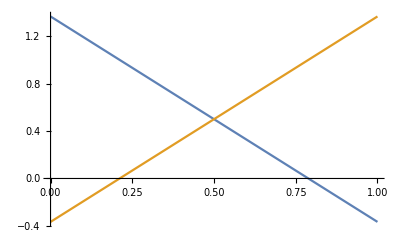

```mathematica
Plot[{f1,f2},{x,0,1}]
```

```mathematica
ML={{Integrate[f1,{x,-1,0}],Integrate[f2,{x,-1,0}]},
{Integrate[f1,{x,0,1}],Integrate[f2,{x,0,1}]}};
MR={{Integrate[f1,{x,0,1}],Integrate[f2,{x,0,1}]},
{Integrate[f1,{x,1,2}],Integrate[f2,{x,1,2}]}};
```

```mathematica
Simplify[ML]
Simplify[MR]
```

{{1/2+√3,1/2-√3},{1/2,1/2}}

{{1/2,1/2},{1/2-√3,1/2+√3}}

```mathematica
InvML=Simplify[Inverse[ML]]
InvMR=Simplify[Inverse[MR]]
```

{{1/(2 √3),1-1/(2 √3)},{-1/(2 √3),1/6 (6+√3)}}

{{1/6 (6+√3),-1/(2 √3)},{1-1/(2 √3),1/(2 √3)}}

```mathematica
fp1=Function[x,Evaluate[f1]];fp2=Function[x,Evaluate[f2]];
I11={{fp1[1]*fp1[1],fp1[1]*fp2[1]},
{fp2[1]*fp1[1],fp2[1]*fp2[1]}};
I1={{Integrate[f1*f1,{x,0,1}],Integrate[f1*f2,{x,0,1}]},
{Integrate[f2*f1,{x,0,1}],Integrate[f2*f2,{x,0,1}]}}
I2={{Integrate[f1*D[f1,x],{x,0,1}],Integrate[f1*D[f2,x],{x,0,1}]},
{Integrate[f2*D[f1,x],{x,0,1}],Integrate[f2*D[f2,x],{x,0,1}]}};
Simplify[I2]
```

{{1/2,0},{0,1/2}}

{{-(√3)/2,(√3)/2},{-(√3)/2,(√3)/2}}

```mathematica
Uinv=Simplify[Inverse[I11-Transpose[I2]]]
```

{{2/3,1/3-1/(√3)},{1/3+1/(√3),2/3}}